```mathematica
Clear["Global`*"]
Needs["Developer`"]
Needs["CCompilerDriver`"]
Needs["Developer`"]
```

RULE1=1

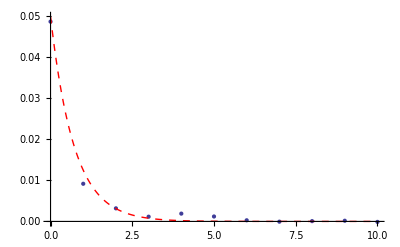

```mathematica
ClearAll[ndlist,raw1,data,RULE1]
RULE1=1;
ndlist=Range[10,90,10];
SetDirectory[NotebookDirectory[]];
raw1=Table[Partition[Import["sol"<>ToString[RULE1]<>"/162_"<>ToString[nd],"Complex128"],2nd+1],{nd,ndlist}];
ResetDirectory[];
ClearAll[n]
n=1;
Print["RULE1=",RULE1];
(data=Table[Table[{m,raw1⟦i,n,m+ndlist⟦i⟧+1⟧},{m,0,ndlist⟦i⟧}],{i,Length[ndlist]}]//Re)//ListLinePlot[#,PlotRange->All,PlotMarkers->Automatic,PlotLegends->ndlist]&;
raw1⟦9,n⟧//Re//ListPlot[#,PlotRange->Automatic]&;
Show[
i=1;Table[{m,raw1⟦i,n,m+ndlist⟦i⟧+1⟧},{m,0,ndlist⟦i⟧}]//Re//ListPlot[#,PlotRange->All]&,
Plot[0.05 0.5^(2m),{m,0,10},PlotRange->All,PlotStyle->{Dashed,Thick,Red}]
]
```

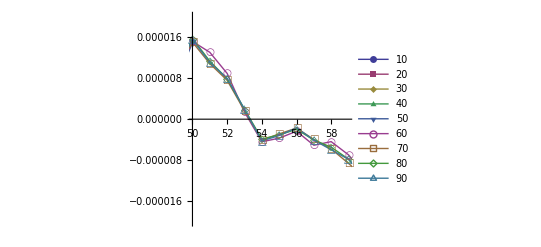

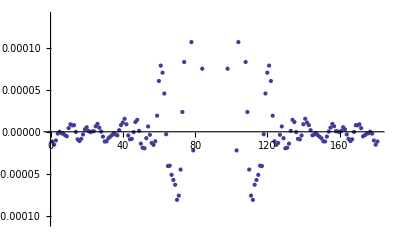

```mathematica
ClearAll[ndlist,raw]
ndlist=Range[10,90,10];
SetDirectory[NotebookDirectory[]];
raw=Table[Partition[Import["sol2/162_"<>ToString[nd],"Complex128"],2nd+1],{nd,ndlist}];
ResetDirectory[];
ClearAll[n]
n=20;
Table[Table[{m,raw⟦i,n,m+ndlist⟦i⟧+1⟧},{m,0,ndlist⟦i⟧}],{i,Length[ndlist]}]//Re//ListLinePlot[#,PlotRange->{{50,59},{-0.00002,0.00002}},PlotMarkers->Automatic,PlotLegends->ndlist]&
raw⟦9,n⟧//Re//ListPlot[#,PlotRange->Automatic]&
```